## Unit conversion factors

```mathematica
C2K[TC_]:=QuantityMagnitude@UnitConvert[Quantity[TC,"DegreesCelsius"],"Kelvins"];
K2C[TK_]:=QuantityMagnitude@UnitConvert[Quantity[TK,"Kelvins"],"DegreesCelsius"];
C2F[TC_]:=QuantityMagnitude@UnitConvert[Quantity[TC,"DegreesCelsius"],"DegreesFarenheit"];
F2C[TF_]:=QuantityMagnitude@UnitConvert[Quantity[TF,"DegreesFarenheit"],"DegreesCelsius"];
```

```mathematica
au2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"Hartrees"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2au=1/au2kcal;
ev2kcal=QuantityMagnitude[UnitConvert[Quantity[1,"ElectronVolts"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]];
kcal2ev=1/ev2kcal;
ev2cm=QuantityMagnitude@UnitConvert[Quantity[1,"ElectronVolts"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2ev=1/ev2cm;
au2ev=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"],"ElectronVolts"];
ev2au=1/au2ev;
au2joule=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"],"Joules"];
joule2au=1/au2joule;
au2cm=QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"];
cm2au=1/au2cm;
```

## Universal constants

```mathematica
h=QuantityMagnitude@Entity["PhysicalConstant","PlanckConstant"]["Value"]; (* in Joule × seconds *)
kb=QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"];
kB=QuantityMagnitude@Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
NAvogadro=QuantityMagnitude@Entity["PhysicalConstant","AvogadroConstant"]["Value"];
R=kB×NAvogadro;
elcharge=QuantityMagnitude@Entity["PhysicalConstant","ElementaryCharge"]["Value"];
F=QuantityMagnitude@Entity["PhysicalConstant","FaradayConstant"]["Value"];
ε0=QuantityMagnitude@Entity["PhysicalConstant","ElectricConstant"]["Value"];
```

## Reduction potentials (V)

```mathematica
EY[E0_,pH_,pKa_]:=E0+0.0552Log[10,1+10^-pH/10^-pKa];
EFY[E0_,pH_,pKa_]:=E0+0.0557Log[10,1+10^-pH/10^-pKa];
```

```mathematica
EY[0.749,8.2,11.3]
```

0.920139

```mathematica
EFY[1.07,8.2,7.9]
```

1.07983

```mathematica
EFY[1.008,8.2,7.2]
```

1.01031

## TST rate constants (s^-1)

```mathematica
kTST[κ_,T_,Ga_]:=κ(kb T au2joule)/h Exp[-(Ga kcal2au)/(kb T)]/Quantity[1,"Seconds"];
Gact[κ_,T_,kobs_]:=-kb T(Log[kobs]-Log[κ]-Log[(kb T au2joule)/h])au2kcal×Quantity[1,"kcal/mole"];
```

```mathematica
ScientificForm[Gact[1.0,298,43.],ExponentFunction->(If[-2<#<2,Null,#]&)]
```

15.2168 kcal_th/mol

```mathematica
31.11-16.27
```

14.84

```mathematica
ScientificForm[kTST[1.0,298,19.7179]]
```

2.15004×10^-2 per second

```mathematica
kTST[1,298,3.1]
```

3.30814×10^10 per second

```mathematica
kTST[1,298,4.0]
```

7.23681×10^9 per second

```mathematica
kTST[1,298,4.2]
```

5.16265×10^9 per second

```mathematica
kTST[1,298,12.3]
```

5923.01 per second

```mathematica
kTST[1,298,14.6]
```

121.838 per second

```mathematica
kTST[1,298,26]
```

5.31273611×10^-7 per second

## Free Energy Diagram

```mathematica
Clear[FEdiagram]
```

```mathematica
FEdiagram[species_,title_,OptionsPattern[{NCycles->1,EnergyRange->All,LabelSize->16}]]:=Module[{energyRange,labelSize,nCycles,nSpecies,sEnergies,sNames,dG,xS,lineXY,connections},
energyRange=OptionValue[EnergyRange];
labelSize=OptionValue[LabelSize];
nCycles=OptionValue[NCycles];
nSpecies=nCycles*Length[species]-nCycles+1;
sNames=species⟦All,1⟧;
Do[
AppendTo[sNames,Drop[species⟦All,1⟧,1]],
{n,1,nCycles-1}
];
sNames=Flatten[sNames];
dG=species⟦-1,2⟧-species⟦1,2⟧;
sEnergies=species⟦All,2⟧;
Do[
AppendTo[sEnergies,Map[#+n*dG&,Drop[species⟦All,2⟧,1]]],
{n,1,nCycles-1}
];
sEnergies=Flatten[sEnergies];
xS=Range[0,5×(nSpecies-1),5];
lineXY=Table[{{xS⟦i⟧-1,sEnergies⟦i⟧},{xS⟦i⟧+1,sEnergies⟦i⟧}},{i,1,nSpecies}];
connections=Table[{{xS⟦i⟧+1,sEnergies⟦i⟧},{xS⟦i+1⟧-1,sEnergies⟦i+1⟧}},{i,1,nSpecies-1}];
Graphics[
{
Black,Thickness[0.004],Table[Line[lineXY[[i]]],{i,1,nSpecies}],
Dotted,Thick,Table[Line[connections[[i]]],{i,1,nSpecies-1}],
Black,FontSize->labelSize,Table[{Text[sNames[[i]],{xS[[i]],sEnergies[[i]]+1.5},FormatType->StandardForm]},{i,1,nSpecies}]
},
PlotRange->energyRange,
ImageSize->Full,
Axes->False,Frame->True,
LabelStyle->{Black,18},
FrameLabel->{"— Reaction Path ⟶","Energy, kcal/mol"},
FrameTicks->{None,Automatic},
PlotLabel->title,
FrameStyle->Directive[Black,Thickness[Medium]]
]
];
```

```mathematica
fig10={{"I_1",-21.81},{"TS_1",-21.81},{"I_2",-31.11},{"TS_2",-20.22},{"I_3",-20.22},{"TS_3",-16.27},{"I_4",-16.27},{"TS_4",-16.27},{"I_5",-32.31},{"TS_5",-24.17},{"I_6",-24.17},{"TS_6",-24.17},{"I_1",-30.32}};
```

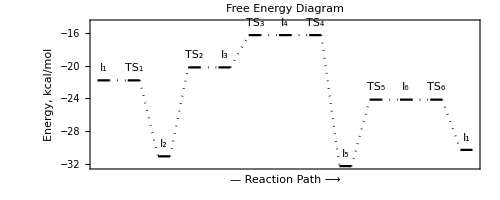

```mathematica
FEdiagram[fig10,"Free Energy Diagram",NCycles->1]
```

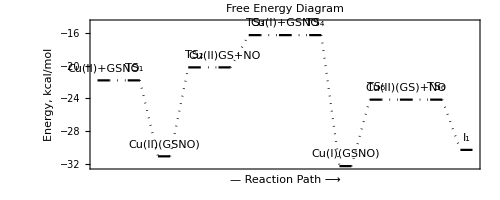

```mathematica
fig10n={{"Cu(II)+GSNO",-21.81},{"TS_1",-21.81},{"Cu(II)(GSNO)",-31.11},{"TS_2",-20.22},{"Cu(II)GS+NO",-20.22},{"TS_3",-16.27},{"Cu(I)+GSNO",-16.27},{"TS_4",-16.27},{"Cu(I)(GSNO)",-32.31},{"TS_5",-24.17},{"Cu(II)(GS)+NO",-24.17},{"TS_6",-24.17},{"I_1",-30.32}};
FEdiagram[fig10n,"Free Energy Diagram",NCycles->1,LabelSize->12]
```

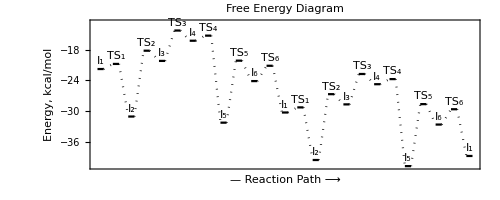

```mathematica
fig10p={{"I_1",-21.81},{"TS_1",-20.81},{"I_2",-31.11},{"TS_2",-18.22},{"I_3",-20.22},{"TS_3",-14.27},{"I_4",-16.27},{"TS_4",-15.27},{"I_5",-32.31},{"TS_5",-20.17},{"I_6",-24.17},{"TS_6",-21.17},{"I_1",-30.32}};
FEdiagram[fig10p,"Free Energy Diagram",NCycles->2]
```

## Energetic Span Model for Catalytic Cycles

```mathematica
TOF[T_,diagram_]:=Module[
{nI,G0,Gf,dG,RT,kTh,GI,GT,dGp,XI,XTS,Δ,M,iTDI,iTDTS,TDI,TDTS,δE,dRxy,dPxy,pni},
RT=kb T au2kcal;
kTh=(kb T au2joule)/h;
Gf=diagram⟦-1⟧;
G0=diagram⟦1,1⟧;
dG=Gf-G0;
nI=Length[diagram]-1;
pni[n_,i_]:=Piecewise[{{i-n+1,n≤i≤nI},{i-n+1+nI,1≤i≤n-1}}];
GI=diagram⟦Range[nI],1⟧;
GT=diagram⟦Range[nI],2⟧;
dGp=Table[If[i>j,dG,0],{i,1,nI},{j,1,nI}];
Δ=kTh (Exp[-dG/RT]-1);
M=Sum[Exp[(GT⟦i⟧-GI⟦j⟧-dGp⟦i,j⟧)/RT],{i,1,nI},{j,1,nI}];
XI=Table[ScientificForm[Sum[Exp[(GT⟦i⟧-GI⟦j⟧-dGp⟦i,j⟧)/RT],{i,1,nI}]/M,6,ExponentFunction->(If[-2<#<1,Null,#]&)],{j,1,nI}];
XTS=Table[ScientificForm[Sum[Exp[(GT⟦i⟧-GI⟦j⟧-dGp⟦i,j⟧)/RT],{j,1,nI}]/M,6,ExponentFunction->(If[-2<#<1,Null,#]&)],{i,1,nI}];
iTDI=Ordering[XI]⟦-1⟧;
iTDTS=Ordering[XTS]⟦-1⟧;
TDI=GI⟦iTDI⟧;
TDTS=GT⟦iTDTS⟧;
δE=If[iTDTS>iTDI,TDTS-TDI,TDTS-TDI+dG];
dRxy=Table[If[pni[n,iTDTS]>pni[n,iTDI],"[R("<>ToString[n]<>")]",1],{n,1,nI}];
dPxy=Table[If[pni[n,iTDTS]<pni[n,iTDI],"[P("<>ToString[n]<>")]",1],{n,1,nI}];
Grid[{
Prepend[Range[nI],"States"],
Prepend[GI,"G(I), kcal/mol"],
Prepend[GT,"G(TS), kcal/mol"],
Prepend[XI,"X(I)"],
Prepend[XTS,"X(TS)"],
Prepend[dRxy,"dR(TDI→TDTS)"],
Prepend[dPxy,"dP(TDI→TDTS)"],
{"ΔG(cycle), kcal/mol",ScientificForm[dG,6,ExponentFunction->(If[-2<#<3,Null,#]&)],SpanFromLeft},
{"δE, kcal/mol",ScientificForm[δE,6,ExponentFunction->(If[-2<#<3,Null,#]&)],SpanFromLeft},
{"TOF, s^-1",ScientificForm[Δ/M,6,ExponentFunction->(If[-2<#<1,Null,#]&)],SpanFromLeft},
{Style[" TDI and TDTS are shown in Red ",Red,Background->White],SpanFromLeft}
},Frame->All,Background->{{1->Gray},{1->Gray}},ItemStyle->{1->White,1->White,{{2,iTDI+1}->{Red,Bold},{3,iTDTS+1}->{Red,Bold},{4,iTDI+1}->{Red,Bold},{5,iTDTS+1}->{Red,Bold}}}]
];
```

```mathematica
fig10={{-21.81,-21.81},{-31.11,-20.22},{-20.22,-16.27},{-16.27,-16.27},{-32.31,-24.17},{-24.17,-24.17},-30.32};
TOF[298,fig10]
```

States | 1 | 2 | 3 | 4 | 5 | 6
G(I), kcal/mol | -21.81 | -31.11 | -20.22 | -16.27 | -32.31 | -24.17
G(TS), kcal/mol | -21.81 | -20.22 | -16.27 | -16.27 | -24.17 | -24.17
X(I) | 1.51318×10^-7 | 0.999989 | 5.15849×10^-9 | 2.85574×10^-17 | 1.04588×10^-5 | 4.6737×10^-12
X(TS) | 2.13247×10^-10 | 3.22159×10^-9 | 0.499996 | 0.499996 | 8.04103×10^-7 | 6.9045×10^-6
dR(TDI→TDTS) | [R(1)] | [R(2)] | 1 | 1 | [R(5)] | [R(6)]
dP(TDI→TDTS) | 1 | 1 | [P(3)] | [P(4)] | 1 | 1
ΔG(cycle), kcal/mol | -8.51 |  |  |  |  | 
δE, kcal/mol | 14.84 |  |  |  |  | 
TOF, s^-1 | 4.06197×10^1 |  |  |  |  | 
 TDI and TDTS are shown in Red  |  |  |  |  |  |

```mathematica
-31.11+21.81+(-16.27+31.11)
```

5.54

## Equilibrium constants

```mathematica
Keq[T_,dG_]:=Exp[-(dG kcal2au)/(kb T)];
```